# What Popularity tells us about a Wikipedia Sub-Graph?

## About this work

Studying the popularity time series of two Wikipedia pages and their correlation, can we say if two pages are linked? And how strong is their link?

Characteristics of The Wikipedia Sub-Graph
The graph in analysis is extracted starting from a central page and considering only English pages. We considered a recent event that involves the central page. We considered all the out-links until the second neighbors, and we selected all the links with at least 2 repetitions. Multiple links are very common and we used this as a measure of the strength of the connection, the Links Multiplicity. We obtained a weighted directed Graph of 3126 Edges and 2164 Vertices.

General Characteristics of Popularity Time Series
Looking at the time series we observed a global behavior, we studied an independent set of 10000 pages in a time window of two months. We saw a weekly effect,  there is weekly fluctuation of the number of visitors, about 20-30%. We calculated  7 daily coefficient in order to correct Popularity and reduce the overestimation of correlations. Looking at an independent set of 1000 pages in a time window of a year, we observed a seasonal effect, but in our time window this is negligible.

What happens when there is an Event? Does Popularity diffuse?
I chose a recent event with a peak around the release date of the movie “Star Trek Into Darkness” (May 16th 2013). I built the weighted sub-graph of Wikipedia English pages, starting from the page of the movie. I collected all the time series of this pages in a time window of two month, around the Event. Looking at the time series we observed that, at this daily resolution, there is no propagation of Popularity, there is no delay between two time series. With this data we can’t consider to study a dynamic. And also we can’t study causal relations. For this reason we decided to study the relation between different pages Popularity with the Pearson Correlation.

Can we predict the real connections of the Graph from Popularity?
The correlations between two time series imply a symmetric Graph: 
N_Links ( v , u ) ~  1  / ( 1 - Correlation ( v , u ) )
We observed an interesting relation between the total number of links of a page and its average Popularity:  
N_Links( v ) ~ Popularity ( v )^0.5
Our hypothesis is a prediction rule of this form:
Multiplicity ( u , v ) ~ [ 1 / (1 - Correlation ( u , v ) ]^a [ Popularity ( u ) ]^b [ Popularity ( v ) ]^c
We tested our prediction rules with different coefficients and we defined an error measure.

## The Wikigraph

### Useful Functions

### Starting from an initial Wikipedia Page, this group of functions built the weighted graph of depth 2 (we consider only links with multiplicity > 1). Multiplicity is our weight.

#### Built the Graph

```mathematica
initialTitle= "Star_Trek_Into_Darkness";
```

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
cleanlinks[links_] := Module[
	{cleanedlinks},
	cleanedlinks = Select[
		links,
		StringMatchQ[#, "http://en.wikipedia.org/wiki/"~~Except[":"]..] &
	];
	cleanedlinks = Select[ Gather[DeleteCases[cleanedlinks,"http://en.wikipedia.org/wiki/Main_Page"]], Length[#] > 1 &];
	Tally@Flatten[cleanedlinks]
	(*First /@ cleanedlinks*)
]
(*this function will consider links multiplicity and links with at least 2 repetitions *)
```

```mathematica
importFirstLevelLinks[init_]:= cleanlinks @ 
	Import["http://en.wikipedia.org/wiki/"<>init, "Hyperlinks"]
(* this output is a list of weighted links with their multiplicity *)
```

```mathematica
createFirstLevelWeightedEdges[init_,weightedlinks_]:=
{init,Last@StringSplit[#[[1]],"/"],#[[2]]}& /@ weightedlinks
```

```mathematica
findFirstNeighbors[firstLevelLinks_]:= Last@StringSplit[#,"/"]& /@firstLevelLinks[[All,1]]
```

```mathematica
importSecondLevelLinks[firstLevelLinks_]:= (cleanlinks @ Import[#,"Hyperlinks"])& /@ firstLevelLinks[[All,1]]
```

```mathematica
createSecondLevelWeightedEdges[firstNeighbors_,secondLevelLinks_]:=
	Module[{secondNeighbors,secondNeighborsWeighted},
		secondNeighbors=Map[Last[StringSplit[#,"/"]]&,secondLevelLinks[[All,All,1]],{2}];
		secondNeighborsWeighted=Transpose[{secondNeighbors[[#]],secondLevelLinks[[#,All,2]]}]& /@ Range[1,Length[secondNeighbors]];
		Flatten[Outer[
			Flatten[{#1,#2}]&,{firstNeighbors[[#]]},{secondNeighborsWeighted[[#]]},2]& /@ Range[1,Length[firstNeighbors]],3] 
]
```

```mathematica
createTheGraph[init_]:=Module[{firstLevel,secondLevel},
	firstLevel=importFirstLevelLinks[init];
	secondLevel=importSecondLevelLinks[firstLevel];
	Flatten[{createFirstLevelWeightedEdges[init,firstLevel],createSecondLevelWeightedEdges[findFirstNeighbors[firstLevel],secondLevel]},1]


]
```

#### Remove Self Loops

```mathematica
NoSelfLoopGraph[EdgesList_]:= DeleteCases[EdgesList,{a_,a_,__}]
```

#### Correct Multiplicity: remove Multi Edges and update Weights

```mathematica
NewGraphWithCorrectMultiplicity[Edges_]:=Module[{unweighted,repetitions,positions,
	replaceIndices,deleteIndices,updates,subs,checkedFirst,checkedFinal},
	unweighted=Edges[[All,;;2]];
	repetitions=Select[Tally[unweighted],(#[[2]]>1)&];
	positions=Position[unweighted,#[[;;2]]]&@@@ repetitions;
	replaceIndices=positions[[All,1]];
	deleteIndices=positions[[All,2]];
	updates=Partition[Flatten[{Edges[[#1[[1]],;;2]],Edges[[#1[[1]],3]]+Edges[[#1[[1]],3]]}&/@ positions],3];
	subs=Map[#1[[1,1]]->#[[2]]&  ,Transpose[{replaceIndices,updates}]];
	checkedFirst=ReplacePart[Edges,subs];
	checkedFinal=Delete[checkedFirst,deleteIndices]

(*this function controls and corrects repetitions in the graph, just use it once*)
]
```

### Operations on the Graph

#### Static visualization with Weights or Ranks

```mathematica
FancyRankingGraph[list_,ranks_,title_,center_]:=
	Graph[DirectedEdge@@@ list,
		VertexSize->ranks,GraphHighlight->{center},
		PlotLabel->Framed[Style[title,15,"Arial"],
		Background->LightBlue],VertexSize->1,ImageSize->700,GraphLayout->"SpringElectricalEmbedding",
		VertexLabels->{center->Framed[Style[center,15,"Arial"],Background->White]}
]
```

```mathematica
NormRankings[rankings_]:=
With[{mean=Mean[rankings[[All,2]]]},

(#->N[#2/mean]& @@@ rankings)
]
```

```mathematica
ExtractWeightedAjdacencyMatrix[listWeightedEdges_, listVertices_]:=
With[{l=Position[StarTrekNet,{listVertices[[#[[1]]]],listVertices[[#[[2]]]],__}]},
	If[Length[l]≠0,StarTrekNet[[l[[1,1]],3]],0]]&/@ Tuples[Range[1,Length[listVertices]],{2}]
```

#### Dynamic visualization with Popularity

```mathematica
AssignDynamicWeights[Vertices_,TimeSeries_]:=
	MapThread[#1 -> Flatten[#2[[All,All,2]]] &, {Vertices,TimeSeries}]
```

```mathematica
PopWeightedGraph[list_,weights_,title_,center_]:=Graph[DirectedEdge@@@ list,
	VertexSize->weights,GraphHighlight->{center},
	PlotLabel->Framed[Style[title,15,"Arial"],
	Background->LightBlue],VertexSize->1,ImageSize->700,GraphLayout->"SpringElectricalEmbedding",
	VertexLabels->{center->Framed[Style[center,15,"Arial"],Background->White]}
]
```

```mathematica
DynamicPopularity[Edges_,popweights_]:=Manipulate[
	With[
		{mean = Mean[Flatten[popweights[[All, 2]]]]},
		PopWeightedGraph[Edges,#1->N[#2[[w]]/ mean]&@@@ popweights
		,"Avatar, popularity","Avatar_%282009_film%29"]
	]
	,{{w,1},1, Length[popweights[[1,2]]], 1}
]
```

## Wikigraph of our Data Set

#### Star Trek Wikigraph: 3126 Edges, 2164 Vertices

We select the most relevant links in each page, starting from "Star Trek Into Darkness", and we take pages until its second neighbors. We consider multiplicity of links as a measure of their importance. We filter pages using Multiplicity > 1.

```mathematica
StarTrekNet=NewGraphWithCorrectMultiplicity[Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/startrekNetwork/allStarTrekWeighted.tsv","TSV"]];
```

#### Edge Multiplicity

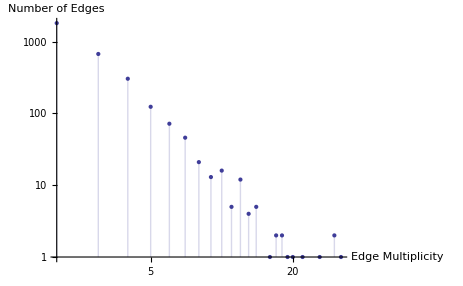

```mathematica
ListLogLogPlot[Tally[StarTrekNet[[All,3]]],Filling->Axis,PlotRange->All,AxesLabel->{"Edge Multiplicity","Number of Edges"}]
```

I consider the unweighted graph:

```mathematica
UnweightedST=StarTrekNet[[All,;;2]];
```

```mathematica
STGraph=Graph[DirectedEdge@@@UnweightedST];
```

```mathematica
STVertices=VertexList[STGraph];
```

### K-Cores decomposition

```mathematica
Length[VertexList[STGraph]]
```

2164

```mathematica
kcores=Map[KCoreComponents[STGraph,#]& , Range[1,12]];
```

```mathematica
Length[Flatten[#]]& /@ kcores
```

{2164,288,139,94,72,61,54,51,42,34,33,22}

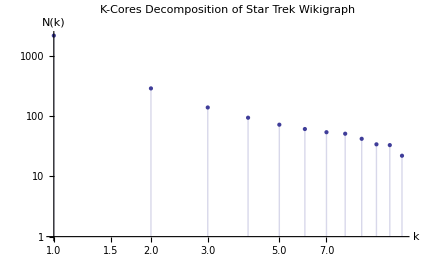

```mathematica
ListLogLogPlot[Transpose[{Range[1,12],Length[#]& @@@ kcores}],PlotLabel->"K-Cores Decomposition of Star Trek Wikigraph", PlotRange->All,AxesLabel->{"k","N(k)"},Filling->Axis]
```

```mathematica
Subgraph[STGraph,KCoreComponents[STGraph,2],PlotLabel->"2-Core of the Wikigraph"]
```

-Graphics-

#### Page Rank

```mathematica
Needs["GraphUtilities`"]
```

```mathematica
STRanks=PageRanks[STGraph];
```

```mathematica
meanRanks=Mean[STRanks[[All,2]]]
```

0.000462107

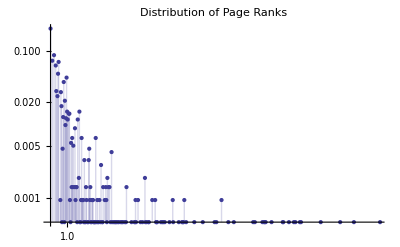

```mathematica
ListLogLogPlot[Transpose[{Tally[N[Round[(1000*STRanks[[All,2]]/ meanRanks)]/1000]][[All,1]],Tally[N[Round[(1000*STRanks[[All,2]]/ meanRanks)]/1000]][[All,2]]/2164.}],Filling->Axis,PlotLabel->"Distribution of Page Ranks",PlotRange->All]
```

```mathematica
STNormRanks= NormRankings[STRanks];
```

```mathematica
STVertices=VertexList[STGraph];
```

#### IN Degree and OUT Degree in the Star Trek Wikigraph

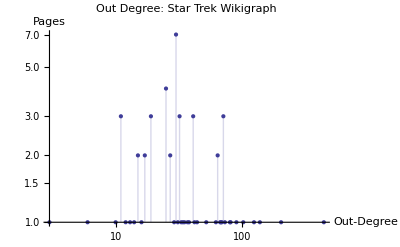

```mathematica
ListLogLogPlot[Tally[VertexOutDegree[STGraph]],Filling->Axis,PlotRange->All,PlotLabel->"Out Degree: Star Trek Wikigraph",AxesLabel->{"Out-Degree","Pages"}]
```

This depends on how the graph was built, but we can roughly see a power law behavior in the InDegree plot.

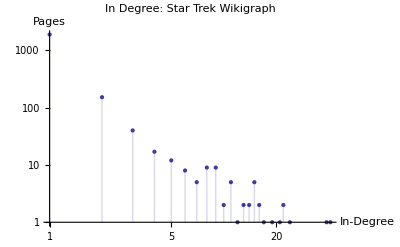

```mathematica
ListLogLogPlot[Tally[VertexInDegree[STGraph]],Filling->Axis,PlotRange->All,PlotLabel->"In Degree: Star Trek Wikigraph",AxesLabel->{"In-Degree","Pages"}]
```

#### Average Popularity of each page

```mathematica
STPop=N[cleanedSTTimeSeries[[All,;;2,All,2]]/Mean[Flatten[cleanedSTTimeSeries[[All,;;2,All,2]]]]];
```

```mathematica
meansSTPop=N@Mean[Flatten[cleanedSTTimeSeries[[#,;;2,All,2]]]]& /@ Range[1,Length[cleanedSTTimeSeries]];
```

```mathematica
bigmean=Mean[meansSTPop]
```

1807.9

```mathematica
meansSTPopNorm=meansSTPop/ bigmean;
```

```mathematica
Export["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/meansSTPopNorm.tsv",meansSTPopNorm,"TSV"];
```

```mathematica
meansSTPop=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/meanSTPopNorm2Months.tsv","TSV"];
```

```mathematica
STPopNorm=MapThread[#->#2&,{STVertices,meansSTPop}];
```

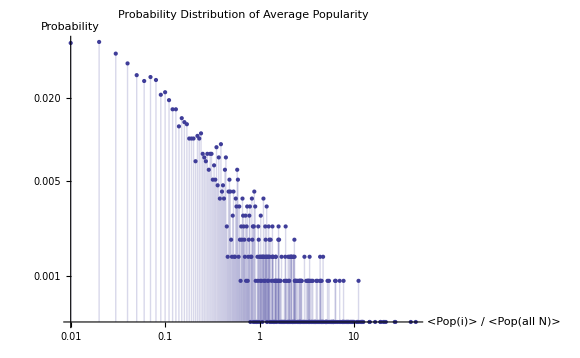

```mathematica
ListLogLogPlot[Transpose[{Tally[N[Round[(100*meansSTPop/ bigmean)]/100]][[All,1]],Tally[N[Round[(100*meansSTPop/ bigmean)]/100]][[All,2]]/2164.}],PlotLabel->"Probability Distribution of Average Popularity",PlotRange->All,Filling->Axis,AxesLabel->{"<Pop(i)> / <Pop(all N)>","Probability"}]
```

#### Histogram of Popularity with logarithmic bins

```mathematica
binMin=0.0001;
binMax=100;
binWidthLog=0.05;
bins={10^Range[Log[10,binMin],Log[10,binMax],binWidthLog]};
```

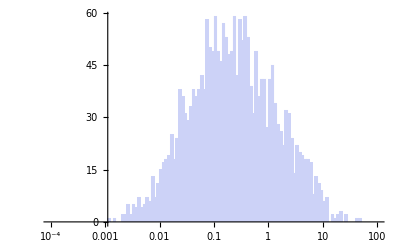

```mathematica
Histogram[meansSTPopNorm,{"Log",bins}]
```

```mathematica
list=HistogramList[meansSTPopNorm,{"Log",bins}];
```

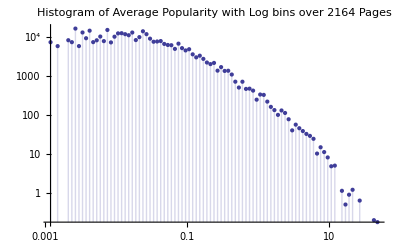

```mathematica
ListLogLogPlot[Transpose[{MovingAverage[#1,2], #2/Differences[#1]} & @@ list],PlotLabel->"Histogram of Average Popularity with Log bins over 2164 Pages",Filling->Axis]
```

#### Are the number of links of a page related to its popularity?

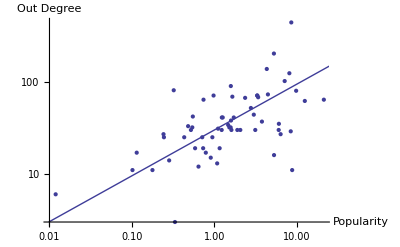

```mathematica
Show[ListLogLogPlot[Transpose[{meansSTPopNorm,VertexOutDegree[STGraph]}],PlotRange->All,AxesLabel->{"Popularity","Out Degree"}], LogLogPlot[30x^0.5,{x,0.01,10000}]]
```

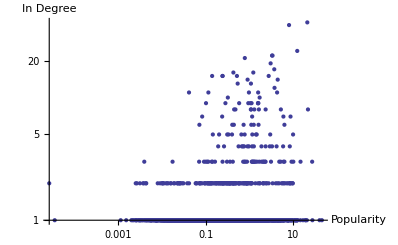

```mathematica
ListLogLogPlot[Transpose[{meansSTPopNorm,VertexInDegree[STGraph]}],PlotRange->All,AxesLabel->{"Popularity","In Degree"}]
```

#### Page Rank VS Average Popularity

Confront between Average Popularity (from May 1st to June 30th 2013) and Page Rank of the Wikigraph.

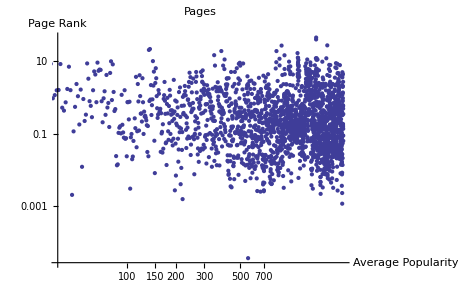

```mathematica
ListLogLogPlot[{meansSTPopNorm,STNormRanks},PlotRange->All,AxesLabel->{"Average Popularity","Page Rank"},PlotLabel->"Pages"]
```

#### Page Rank VS One Day Popularity

Confront between One Day Popularity (June 27th 2013) and Page Rank of the Wikigraph.

```mathematica
OneDayPop= STPop[[All,2,27]];
```

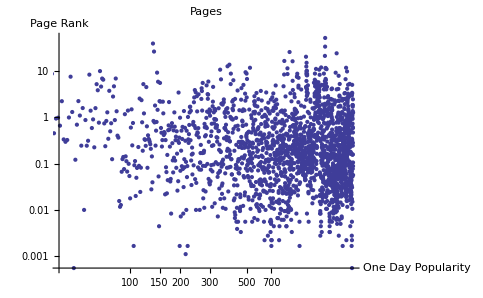

```mathematica
ListLogLogPlot[{OneDayPop,STNormRanks},PlotRange->All,AxesLabel->{"One Day Popularity","Page Rank"},PlotLabel->"Pages"]
```

## Popularity Time Series

### Useful Functions

#### Where? http : // stats.grok.se/json/en/

Given a list of Titles of Wikipedia Pages this function extract the time series for the chosen dates (in months), and print the results on a json file.

```mathematica
importingOnFile[dates_List,pages_,outputfile_]:=
Do[
	(Import["http://stats.grok.se/json/en/"<>#1<>"/"<>pages[[i]], "JSON"]>>>
		"/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/"<>outputfile) & /@ dates
	,
	{i,Length[pages]}]
(*dates_List = {"200910","200911","200910",..} in months, in crescent order, pages = list of vertexes, outputfile= "name.format" *)
```

#### Process and Plot Time Series

This function read from file the time series, knowing how many months.

```mathematica
readingTimeSeries[file_,months_]:= ReadList["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/"<>file]
```

```mathematica
CleanTimeSeries[series_]:={FromDigits /@ StringSplit[#,"-"],#2}& @@@ series[[1,2]]
```

This function cleans imported data and makes them ready to be plotted.

```mathematica
ExtractTimeSeries[imported_List,Nmonths_Integer]:=Partition[CleanTimeSeries[#]& /@ imported,Nmonths]
```

This function is useful to study the average behavior of a random sample of pages.

```mathematica
averageTimeSeries[cleanedTS_]:= N@Mean[Flatten[cleanedTS[[#,All,All,2]]]& /@ Range[1,Length[cleanedTS]]]
```

This function plots the popularity for the selected Vertex:

```mathematica
PlotTimeSeries[series_,opts___]:= DateListPlot[series,Joined ->True,opts]
```

```mathematica
ShowTimeSeries[index_,vertices_,imported_List,Nmonths_Integer]:= 
	PlotTimeSeries[
		ExtractTimeSeries[imported,Nmonths][[index]],
			PlotRange->All,PlotLabel->vertices[[index]
		]
	]
```

This function correct the weekly fluctuation effect:

```mathematica
Corrections[daily_,timeseries_]:=
	Map[#/Flatten[Table[daily,{Round[(Length[#]/7. )+ 1]}]][[;;Length[#]]] &, timeseries,{1}]
```

### What about the Popularity behavior?

#### Download the Time Series

```mathematica
indipendentlinks=Flatten[Table[Import["http://en.wikipedia.org/wiki/Special:Random", "Hyperlinks"],{10000}]];
```

```mathematica
indipendentclean=Select[DeleteDuplicates[indipendentlinks], StringMatchQ[#,"http://en.wikipedia.org/wiki/"~~Except[":"]..]&];
```

```mathematica
indipendentSet=RandomSample[indipendentclean,10000 ];
```

```mathematica
indipendentSet>>> "/Users/Levantina/Documents/WOLFRAM/PROJECT/inidpendentlinks.txt"
```

```mathematica
time= {"201305","201306"};
```

```mathematica
indipendentlinkNameSet=Last @StringSplit[#,"/"]&/@indipendentSet;
```

```mathematica
importingLinksOnFile[time,indipendentlinkNameSet,"bigrandomlinksseries.txt"];
```

```mathematica
bigGE= readingTimeSeries["bigrandomlinksseries.txt",2];
```

```mathematica
cleanBigGE=ExtractTimeSeries[bigGE,2];
```

```mathematica
averages=N@Mean[Flatten[cleanBigGE[[#,All,All,2]]]& /@ Range[1,Length[cleanBigGE]]];
```

```mathematica
firstaverages= N@Mean[Flatten[cleanBigGE[[#,All,All,2]]]& /@ Range[1,5000]];
```

```mathematica
secondaverages= N@Mean[Flatten[cleanBigGE[[#,All,All,2]]]& /@ Range[5000,10000]];
```

```mathematica
normfirst=firstaverages/N@Mean[firstaverages];
```

```mathematica
normsecond= secondaverages/N@Mean[secondaverages];
```

```mathematica
normaverages= averages / N@Mean[averages];
```

```mathematica
weeks=Partition[normaverages,7];
```

#### 10 000 independent Time Series: Weekly Periodicity

We obtain the average behavior per day in two months. What we see is that there is a general effect, due to a weekly periodicity, and we are going to quantify this fluctuation with 7 coefficients. With this coefficients we are going to reduce this effect over the data set that we are going to study. We can say that the Seasonal effect is negligible for a time window of two months, and we assume the effect to be constant over two months, and due to a daily behavior, as we can see in the graphics.

#### Two Months Average Behavior

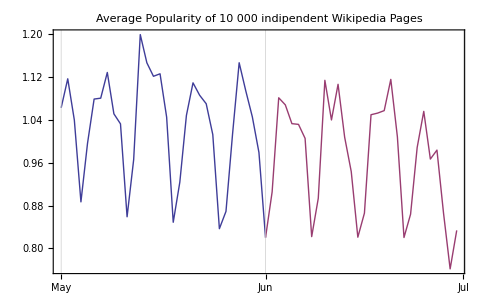

#### Confirm of the Weekly Period and Coefficients

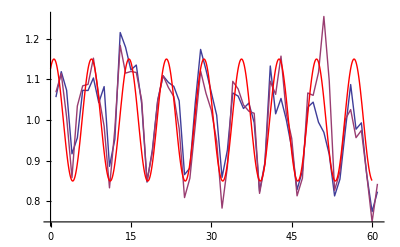

```mathematica
Show[ListLinePlot[{normfirst,normsecond}], Plot[1+0.15Sin[2.Pi/7x+1],{x,0,60}, PlotStyle-> Red]]
```

```mathematica
averagesDaily=N@ Mean[weeks[[All,#]]]& /@ Range[1,7]
```

{1.08612,1.07051,1.00822,0.839358,0.91041,1.07162,1.08735}

#### Weekly Average Behavior

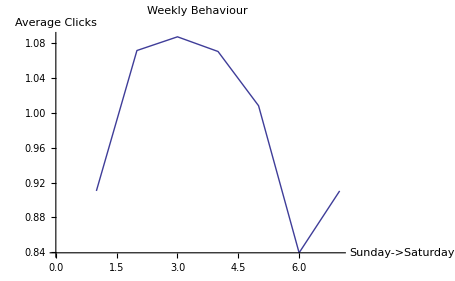

```mathematica
ListLinePlot[Flatten[{averagesDaily[[5;;7]],averagesDaily[[2;;5]]}],PlotLabel->"Weekly Behaviour",AxesLabel->{"Sunday->Saturday","Average Clicks"}]
```

#### 1000 Average Time Series over a year

We can see that the average clicks decrease near Summer, and increase in Autumn. And also we can see a minimum near December/January holidays.

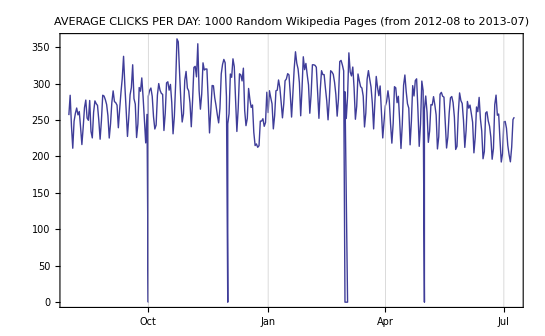

## Popularity Time Series of our Data Set

#### Import Data

```mathematica
importedSTTimeSeries=readingTimeSeries["startrekTimeSeries.json",2];
```

```mathematica
cleanedSTTimeSeries=ExtractTimeSeries[importedSTTimeSeries,2];
```

#### Interesting Event

The movie Star Trek Into Darkness reached a high peak of visitors on May 20th 2013, near the Release Date May 16th 2013.

```mathematica
Max[importedSTTimeSeries[[1,1,2,All,2]]]
```

128702

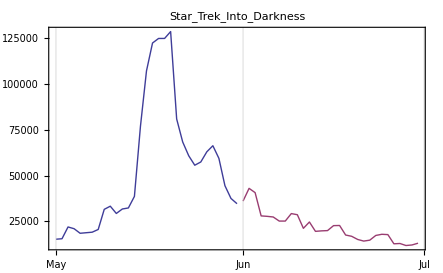

```mathematica
ShowTimeSeries[1,STVertices,importedSTTimeSeries,2]
```

#### Time Series of the others vertices in the Wikigraph

With the Vertex Index we can know its time series:

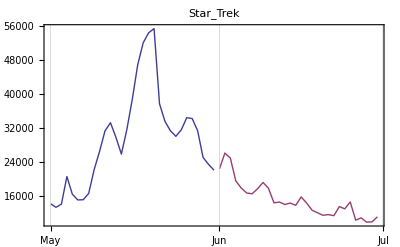
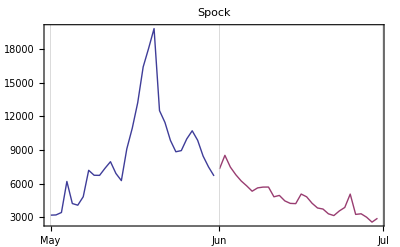
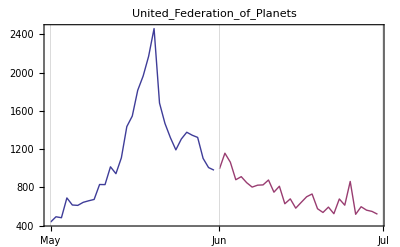
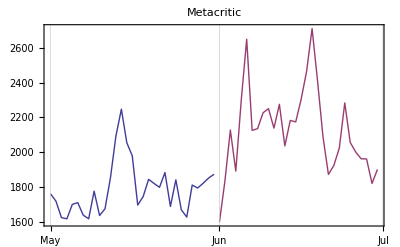
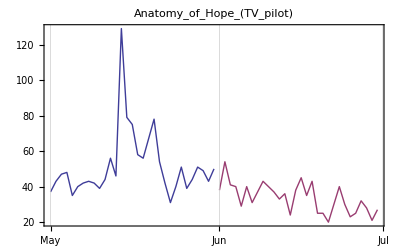
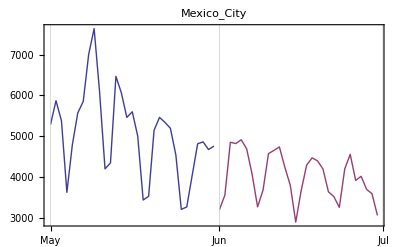
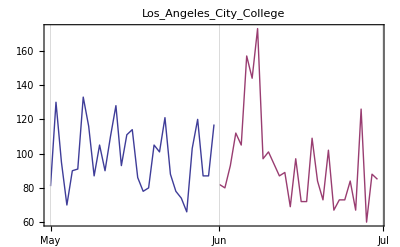
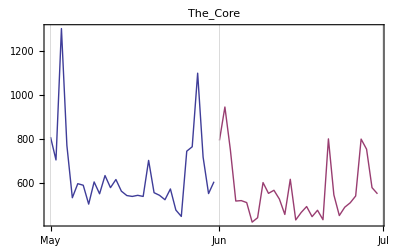

```mathematica
ShowTimeSeries[#,STVertices,importedSTTimeSeries,2]& /@ {7,3         0,40,50,100,150,200,500}
```

#### Given an event, are Popularities Delayed in time?

Popularities for neighbors of “Star Trek Into Darkness”, “”Star Trek (film)”, “Star Trek”, “Spock”, ““James T. Kirk”. They don’t seem delayed in time. For this reason to study correlations we will use the Pearson Correlation.

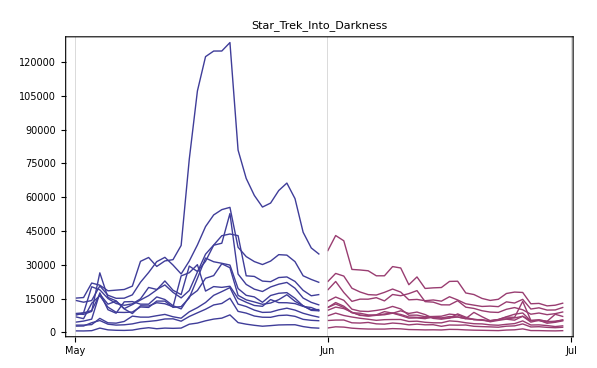

```mathematica
Show[ShowTimeSeries[1,STVertices,importedSTTimeSeries,2],ShowTimeSeries[7,STVertices,importedSTTimeSeries,2],ShowTimeSeries[30,STVertices,importedSTTimeSeries,2],ShowTimeSeries[25,STVertices,importedSTTimeSeries,2],ShowTimeSeries[26,STVertices,importedSTTimeSeries,2],ShowTimeSeries[32,STVertices,importedSTTimeSeries,2],ShowTimeSeries[15,STVertices,importedSTTimeSeries,2],ShowTimeSeries[9,STVertices,importedSTTimeSeries,2],ShowTimeSeries[11,STVertices,importedSTTimeSeries,2],ShowTimeSeries[10,STVertices,importedSTTimeSeries,2]]
```

#### Instant Behavior

Our resolution is of one day, we can’t see a diffusion in this behavior, we can’t consider a dynamic. And also we can’t study causal relations. We can see correlations, but we can’t say if the correlation between two pages exists because of the structure of the network, or because there is a causal connection between the two pages, beyond the network. This two mechanism probably coexist but we can’t see with these data if one is predominant.

## Correlations between Time Series

### Useful Functions

#### Fast Correlation

```mathematica
FastCorrelations[timeseries_]:=Module[{matrix,length},
	length=Length[timeseries[[1]]];
	matrix = If[
				StandardDeviation[#]>0, N[(#-Mean[#])/(StandardDeviation[#]*Sqrt[length])],
				Table[0.,{Length[#]}]] &/@timeseries
    matrix.Transpose[matrix]
]

FastCorrelations2[timeseries_]:= Module[
	{matrix, correlationmatrix, minlengthmatrix, trimmedtimeseries, timeserieslength},
	trimmedtimeseries = Cases[{#}, {Longest[Repeated[0., {0,Infinity}]],x:___} :> x] & /@ timeseries;
	timeserieslength = Length /@ trimmedtimeseries;
	trimmedtimeseries = If[
		StandardDeviation[#]>0,
		(# - Mean[#])/Sqrt[Mean[(#-Mean[#])^2]],
		Table[0., {Length[#]}]
	]& /@ trimmedtimeseries;
	trimmedtimeseries = N@PadLeft[trimmedtimeseries];
	minlengthmatrix = Outer[Min, timeserieslength, timeserieslength];
	correlationmatrix = trimmedtimeseries.Transpose[trimmedtimeseries];
	correlationmatrix/minlengthmatrix
]

realLength[list_] := Length[Cases[{list}, {Longest[Repeated[0., {0,Infinity}]],x:___} :> x]];

realCorrelation[list1_, list2_] := Module[
	{reallength},
	reallength = Min[realLength[list1], realLength[list2]];
	Correlation[Take[list1, -reallength], Take[list2, -reallength]]
];

NotFastCorrelations[timeseries_]:= Outer[realCorrelation, timeseries, timeseries, 1];
```

We can transform the correlation in a distance in the graph:
d(i,j) = Sqrt[2*(1-corr(i,j))]
d= {0 correlated, Sqrt[2] not correlated, 2 anti correlated}

```mathematica
DistancesFromCorrelationMatrix[matrix_]:= Sqrt[2*(1-#)] & /@ matrix
```

#### Adjacency Matrix

Put 0s on the diagonal (for Array Plot Visualization)

```mathematica
removingSelfLoops[length_]:=(-1)*(IdentityMatrix[length]-1)
```

Visualize with the function Graph, and put Infinity to disconnect vertices. Transform a matrix of multiplicity in a matrix with distances.

```mathematica
MyInversion[n_]:=If[n==0,Infinity,1./n]
SetAttributes[MyInversion,Listable]
```

```mathematica
TransformAdjacencyMatrixForGraph[multiplicityMatrix_]:= MyInversion[multiplicityMatrix]
```

```mathematica
InfiniteDiagonal = Map[ If[#==1,Infinity,1]& ,IdentityMatrix[65],{2}];
```

Extract the adjacency matrix from a a list of weighted edges, using the listVertices order.

```mathematica
ExtractWeightedAjdacencyMatrix2[listWeightedEdges_, listVertices_]:=
Module[{position, length},
		length= Length[listVertices];
		(position=Position[StarTrekNet,{STVertices[[#[[1]]]],STVertices[[#[[2]]]],__}];
			If[Length[position]≠0,StarTrekNet[[position[[1,1]],3]],0]) &/@ Tuples[Range[1,length],{2}]]
```

```mathematica
ExtractWeightedAjdacencyMatrix[listWeightedEdges_, listVertices_]:= Module[
	{f, adjmatrix},
	MapIndexed[Set[f[#1], Sequence@@#2 ] &, listVertices];
	adjmatrix=ConstantArray[0, {Length[listVertices], Length[listVertices]}];
	Set[adjmatrix[[f[#1], f[#2]]] , #3] & @@@ listWeightedEdges;
	adjmatrix
]
```

```mathematica
mat=ExtractWeightedAjdacencyMatrix[ StarTrekNet, STVertices];
```

### Evaluation with the daily correction

#### Daily correction for Time Series

We noticed a weekly fluctuation of the visitors on Wikipedia, we found a weekly periodicity. We have a correction for each day of the week. And during the evaluation of the correlations we will consider this 7 coefficients. In order to reduce the overestimating of the correlations.

```mathematica
averagesDaily={1.0861167208459364,1.070509192186192,1.0082207459429013,0.8393580386204945,0.910410111634681,1.0716210490409843,1.0873540902600047}
```

{1.08612,1.07051,1.00822,0.839358,0.91041,1.07162,1.08735}

```mathematica
rightSTPop=Flatten[cleanedSTTimeSeries[[#,;;2,All,2]]]& /@ Range[1,Length[cleanedSTTimeSeries[[All,;;2,All,2]]]];
```

```mathematica
Corrections[daily_,timeseries_]:=
Module[{days=Length[timeseries[[1]]]},
	Map[#/Flatten[Table[daily,{Round[days/7]+1}]][[;;Length[#]]] &, timeseries,{1}]
]
```

```mathematica
PopularityNormal=rightSTPop;
```

```mathematica
PopularityCorrected=Corrections[averagesDaily,rightSTPop];
```

#### Pearson Correlation with Popularity and Corrected Popularity

We have 2164 time series of length 61 days. In order to have a fast evaluation instead of using the build-in function Correlation[ ] I use a function with the Matrix Multiplication ( . )

```mathematica
PopularityNormalMinusAverages=If[StandardDeviation[#]>0,N[(#-Mean[#])/(StandardDeviation[#]*Sqrt[Length[#]])],Table[0.,{Length[#]}]]&/@PopularityNormal;
```

```mathematica
matrixProduct=PopularityNormalMinusAverages.Transpose[PopularityNormalMinusAverages];
```

```mathematica
Export["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/CorrelationsSTNormalTimeSeries.tsv"
,matrixProduct,"TSV"];
```

```mathematica
matrixProductCorrected=FastCorrelations[PopularityCorrected];
```

```mathematica
Export["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/CorrelationsSTCorrectedTimeSeries.tsv",matrixProductCorrected,"TSV"];
```

#### Confront Correlations

We can see that the correction that we used over the time series give us a different correlation, smaller in average of a ~ 24%. We wanted to reduce the effect of the weekly fluctuations, that can bring a higher correlation.

```mathematica
diff=matrixProduct-matrixProductCorrected;
```

```mathematica
Mean[Flatten[diff]]
```

0.0239076

```mathematica
Mean[Flatten[matrixProduct]]
```

0.100801

```mathematica
Mean[Flatten[matrixProductCorrected]]
```

0.0768935

```mathematica
StandardDeviation[Flatten[matrixProduct]]
```

0.226161

```mathematica
StandardDeviation[Flatten[matrixProductCorrected]]
```

0.225873

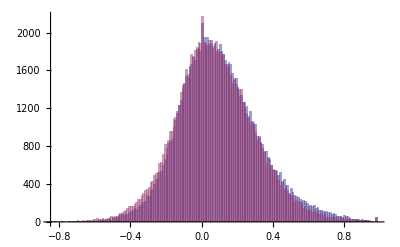

```mathematica
Histogram[{RandomSample[Flatten[matrixProduct],100000], RandomSample[Flatten[matrixProductCorrected],100000]}]
```

## How can we reproduce the real connections in the Graph?

### The Neighborhood Graph of “Star Trek Into Darkness”: first neighbors.

#### The Real Sub-Graph

This is what we want to reproduce.

```mathematica
STNeighGraph=NeighborhoodGraph[STGraph,STVertices[[1]]];
HighlightGraph[NeighborhoodGraph[STGraph,STVertices[[1]],PlotLabel->"Star Trek Into Darkness"],STVertices[[1]]]
```

-Graphics-

#### Data

```mathematica
STNeighborhood=VertexList[NeighborhoodGraph[STGraph,STVertices[[1]]]];
```

```mathematica
edgesSTNeigh=EdgeList[NeighborhoodGraph[STGraph,STVertices[[1]]]];
```

```mathematica
SecondNeighbors=STVertices[[65;;Length[STVertices]]];
```

#### The Real Adjacency Matrix

We build the adjacency matrix of the graph (multiplicity of links will be a measure of their strength):

```mathematica
distanceMatrixCorrected=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/startrekNetwork/distanceMaxtrixCorrected.tsv","TSV"];
```

```mathematica
distanceMatrix65=distanceMatrixCorrected[[;;65,;;65]];
```

This matrix represent the links that we want to reproduce.

```mathematica
ArrayPlot[AdjMatr65,PlotLabel->"Multiedges First Neighbors"]
```

-Graphics-

#### Total Number of Real Links VS Popularity

```mathematica
AdjMatr65=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/startrekNetwork/adjMatrix65.tsv","TSV"];
```

```mathematica
AdjMatr65=Partition[Flatten[AdjMatr65],65];allLinks=(Plus@@AdjMatr65[[All,#]]+Plus@@AdjMatr65[[#,All]] )& /@ Range[1,65];
Max[allLinks]
```

```mathematica
meansSTPopNorm=Flatten@Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/meansSTPopNorm.tsv","TSV"];
```

I find an interesting behavior: Links( v ) ~ Popularity( v )^0.5

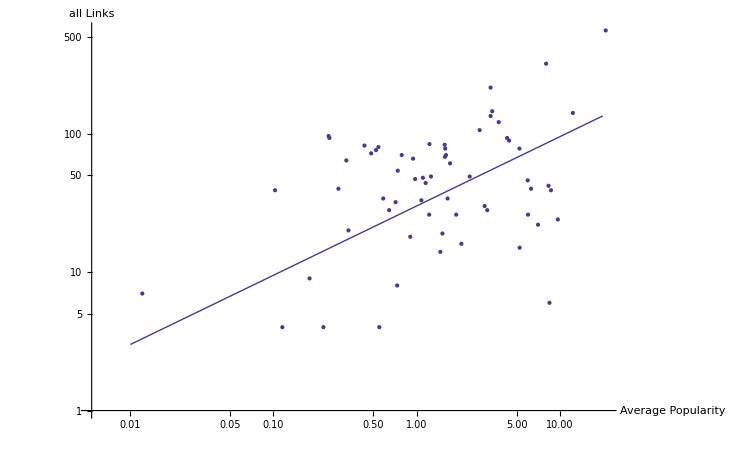

```mathematica
Show[ListLogLogPlot[Transpose[{meansSTPopNorm[[;;65]],allLinks}],AxesLabel->{"Average Popularity","all Links"}],LogLogPlot[30x^0.5,{x,0.01,20}]]
```

We are going to consider this behavior to predict the number of links that connect two pages.

#### Number of Real Links VS Correlation

```mathematica
corrMatrix=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/CorrelationsSTCorrectedTimeSeries.tsv","TSV"];
```

```mathematica
corrMatrixNoSelfCorr=corrMatrix*(-1)*(IdentityMatrix[Length[First[corrMatrix]]]-1);
```

```mathematica
corrMatrix65= corrMatrixNoSelfCorr[[;;65,;;65]];
```

```mathematica
corrMatrix65=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/corrMatrix65.tsv","TSV"];
```

```mathematica
meansSTPopNorm=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/meanSTPopNorm2Months.tsv","TSV"];
```

```mathematica
Show[Histogram[Cases[Transpose[{Flatten[Round[100*corrMatrix65]/100.],Flatten[AdjMatr65]}],Except[{0.,0}]],PlotRange->All],LogLogPlot[1.5+5.x^0.7,{x,0.001,2}]]
```

$Aborted

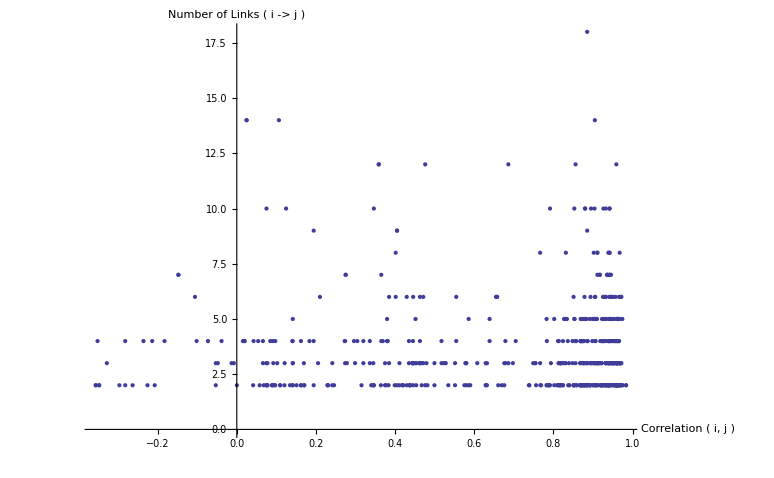

```mathematica
ListPlot[Select[Transpose[{Flatten[corrMatrix65],Flatten[AdjMatr65]}], #[[2]]>0 &], PlotRange->Full,AxesLabel->{"Correlation ( i, j )","Number of Links ( i -> j )"}]
```

### From Correlations to a Graph

#### All Correlations Matrix

We build the adjacency matrix with all the distances d between the vertices (a measure of the correlation):

d = ( 1 - corr [ i , j ] )
corr [ i , j ] = 1 - d

```mathematica
distanceMatrixCorrected=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/startrekNetwork/distanceMaxtrixCorrected.tsv","TSV"];
```

```mathematica
distanceMatrix65=distanceMatrixCorrected[[;;65,;;65]];
```

How the “correlation” matrix look like? We consider:
Multiplicity ( i , j ) ~  1 / ( 1 - corr [ i , j ] )

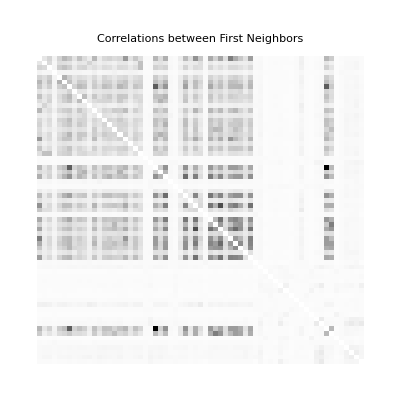

```mathematica
ArrayPlot[1./distanceMatrix65*removingSelfLoops, PlotLabel->"Correlations between First Neighbors"]
```

#### Correlation Matrix with a Threshold

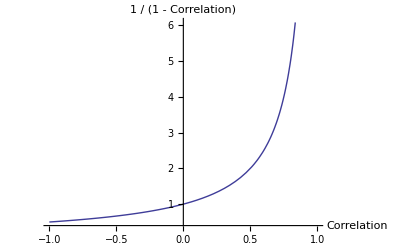

```mathematica
Plot[1./(1-x), {x,-1.,1},AxesLabel->{"Correlation","1 / (1 - Correlation)"}]
```

```mathematica
thresholdInverseDistanceMatrix65=Map[If[#<10,0,#]&, (1./ distanceMatrix65)*removingSelfLoops,{2}];
```

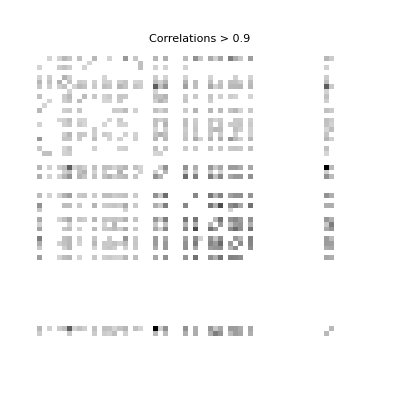

```mathematica
ArrayPlot[thresholdInverseDistanceMatrix65,PlotLabel->"Correlations > 0.9"]
```

#### Matrix of the Square Root of the Popularity Product between each Page

How the popularity matrix look like? If we consider:
Multiplicity ( i , j ) ~ [ Pop ( i ) * Pop ( j ) ] ^ 0.5

```mathematica
PopMatrixSqrt=Outer[Sqrt[#1#2]&,meansSTPopNorm[[;;65]],meansSTPopNorm[[;;65]]];
```

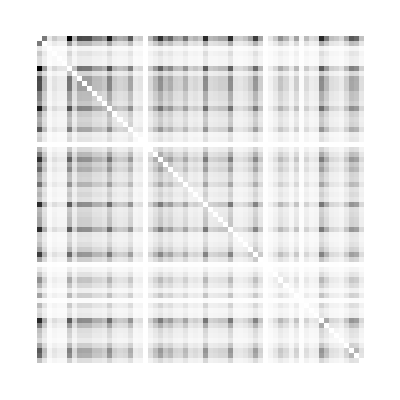

```mathematica
ArrayPlot[PopMatrixSqrt*removingSelfLoops]
```

## Link Prediction

From the correlation between two pages and their popularity value, can we say if there is a link or not? We are going to predict the multiplicity of a link, and we are going to assign a error to this prediction.

Distance [ u , v ]  = ( 1 - corr ( u , v ) )

Adjacency Matrix: 1 / Distances

Multiplicity ( u , v ) ~ [ 1 / (1 - corr ( u , v ) ]^a [ Pop ( u ) ]^b [ Pop ( v ) ]^c

### Functions

#### Prediction Rules

```mathematica
LinkPrediction[d_,popi_,popj_]:= Module[
	{DistThreshold = 20., PopThreshold = 90.},
	If[d > DistThreshold || popi*popj>PopThreshold,
		0.5*d*Sqrt[popi*popj],
		0.
	]
]
```

```mathematica
LinkPredictionLeft[d_,popi_,popj_]:= Module[
	{DistThreshold = 25., PopThreshold = 80.},
	If[d > DistThreshold || popi*popj>PopThreshold,
		0.5*d*Sqrt[popi],
		0.
	]
]
```

```mathematica
LinkPredictionRight[d_,popi_,popj_]:= Module[
	{DistThreshold = 30., PopThreshold = 90.},
	If[d > DistThreshold || popi*popj>PopThreshold,
		0.5*d*Sqrt[popj],
		0.
	]
]
```

```mathematica
LinkPredictionSquare[d_,popi_,popj_]:= Module[
	{DistThreshold = 16., PopThreshold = 80.},
	If[d > DistThreshold || popi*popj>PopThreshold,
		0.5*Sqrt[d]*Sqrt[popi*popj],
		0.
	]
]
```

```mathematica
LinkPredictionSquareLeft[d_,popi_,popj_]:= Module[
	{DistThreshold = 14., PopThreshold = 60.},
	If[d > DistThreshold || popi*popj>PopThreshold,
		0.6*Sqrt[d]*Sqrt[popi],
		0.
	]
]
```

```mathematica
LinkPredictionSquareRight[d_,popi_,popj_]:= Module[
	{DistThreshold = 14., PopThreshold = 60.},
	If[d > DistThreshold || popi*popj>PopThreshold,
		1.*Sqrt[d]*Sqrt[popj],
		0.
	]
]
```

#### Graph Prediction

```mathematica
GraphPrediction[adjMatrix_,popularities_,DistThreshold_,PopThreshold_]:=Map[LinkPrediction[adjMatrix[[#[[1]],#[[2]]]],
popularities[[#[[1]]]],popularities[[#[[2]]]],DistThreshold,PopThreshold]&, 
Table[{i,j},{i,1,Length[adjMatrix[[1]]]},{j,1,Length[adjMatrix[[1]]]}],{2}];
```

```mathematica
GraphPrediction1[correlationMatrix_, popularities_] := Module[
{predictedAdjencyMatrix, a, threshold},
	a = .05;
	threshold = 1.;
	predictedAdjencyMatrix = a/(1.-correlationMatrix)*KroneckerProduct[popularities^0.5, popularities^0.1];
	Threshold[predictedAdjencyMatrix, threshold]
];
```

```mathematica
GraphPrediction2[correlationMatrix_, popularities_] := Module[
{predictedAdjencyMatrix, a, threshold},
	a = 5;
	threshold = 10.;
	predictedAdjencyMatrix = a/(1.-correlationMatrix)*Sqrt[popularities];
	Threshold[predictedAdjencyMatrix, threshold]
];
```

```mathematica
GraphPrediction3[correlationMatrix_, popularitiesMatrix_] := Module[
{predictedAdjencyMatrix, a, threshold},
	a = 5;
	threshold = 20;
	predictedAdjencyMatrix = a/(1.-correlationMatrix)*Sqrt[popularitiesMatrix];
	Threshold[predictedAdjencyMatrix, threshold]
];
```

#### Error Measure

```mathematica
predictionError[realMatrix_, predictedMatrix_] := Sqrt[Mean[Flatten[predictedMatrix-realMatrix]^2]];

predictionError2[realMatrix_, predictedMatrix_] := Sqrt[Mean[Flatten[(predictedMatrix-realMatrix)^2/(realMatrix+1)]]];
```

### Test The Prediction Rules

This prediction rules consider Correlation and Popularity of the pages. If two pages are strongly correlated we put a weighted link between them, proportional to their proximity and the square root of their popularity. Otherwise, if they are not strongly correlated, we consider just their popularity, if their popularity is large, we put a weighted link between them.

```mathematica
corrMatrix=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/CorrelationsSTCorrectedTimeSeries.tsv","TSV"];
```

```mathematica
corrMatrixNoSelfCorr=corrMatrix*(-1)*(IdentityMatrix[Length[First[corrMatrix]]]-1);
```

```mathematica
corrMatrix65=corrMatrixNoSelfCorr[[;;65,;;65]];
```

```mathematica
corrMatrix65=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/corrMatrix65.tsv","TSV"];
```

```mathematica
meansSTPopNorm=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/meansSTPopNorm.tsv","TSV"];
```

```mathematica
Dimensions[corrMatrix65]
```

{65,65}

```mathematica
Length[meansSTPopNorm]
```

2164

```mathematica
Export["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/meanSTPopNorm65.tsv",meansSTPopNorm[[;;65]],"TSV"];
```

/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/meanSTPopNorm65.tsv

```mathematica
Clear[GraphPrediction1]
```

```mathematica
predicted=GraphPrediction1[corrMatrix65,Flatten@meansSTPopNorm[[;;65]]];
```

```mathematica
predictionError[AdjMatr65, predicted]
```

```mathematica
Mean[Flatten[predicted - AdjMatr65]]
```

-0.117821

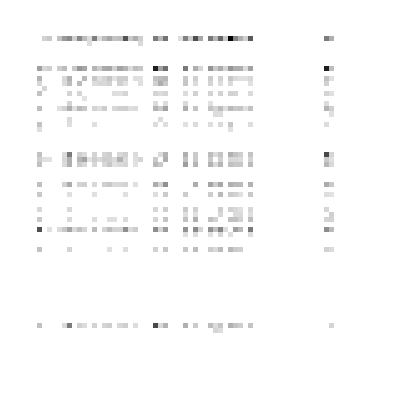

```mathematica
ArrayPlot[predicted]
```

```mathematica
ArrayPlot[AdjMatr65]
```

-Graphics-

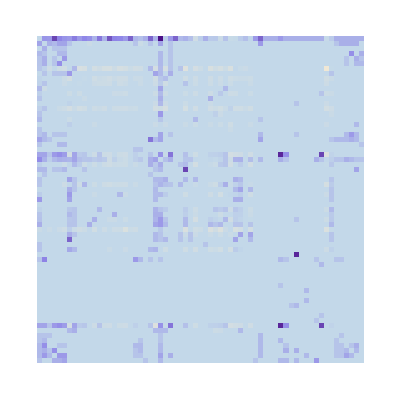

```mathematica
ArrayPlot[predicted-AdjMatr65,ColorFunction->"LakeColors"]
```

```mathematica
WeightedAdjacencyGraph[TransformAdjacencyMatrixForGraph[predicted*removingSelfLoops[65]]]
```

-Graphics-

## Live Prediction

#### Prediction Rule

```mathematica
LinkPrediction1[i_,j_,correlationMatrix_, popularities_] := Module[
{predictedLink, a, threshold},
	a = .05;
	threshold = 1.;
	predictedLink = a/(1.-correlationMatrix[[i,j]])*popularities[[i]]^0.5*popularities[[j]]^0.1;
	Threshold[predictedLink, threshold]
];
```

#### Data

```mathematica
corrMatrix65=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/corrMatrix65.tsv","TSV"];
meansSTPopNorm65=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/meanSTPopNorm65.tsv","TSV"];
AdjMatr65=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/startrekNetwork/adjMatrix65.tsv","TSV"];
AdjMatr65=Partition[Flatten[AdjMatr65],65];
```

### Prediction

```mathematica
STVertices[[;;20]]
```

{Star_Trek_Into_Darkness,J._J._Abrams,Bryan_Burk,Damon_Lindelof,Alex_Kurtzman,Roberto_Orci,Star_Trek,Gene_Roddenberry,Chris_Pine,Zachary_Quinto,Zoe_Saldana,Karl_Urban,Simon_Pegg,John_Cho,Benedict_Cumberbatch,Anton_Yelchin,Bruce_Greenwood,Peter_Weller,Alice_Eve,Michael_Giacchino}

```mathematica
LinkPrediction1[1,12,corrMatrix65,meansSTPopNorm65]
```

{4.3823}

```mathematica
AdjMatr65[[1,12]]
```

8

## Refine the Wikipedia Graph

### Study The Second Neighbors

### In order to better understand the structure of our sub-graph we are going to study some properties of the Second Neighbors of this Graph, in this case they are the Second Neighbors of our Central Page, “Star Trek Into Darkness”. We will find the links that connect the pages to the graph, and we will compare it with the fraction of links that connect this pages outwards the graph.

#### Edge Multiplicity

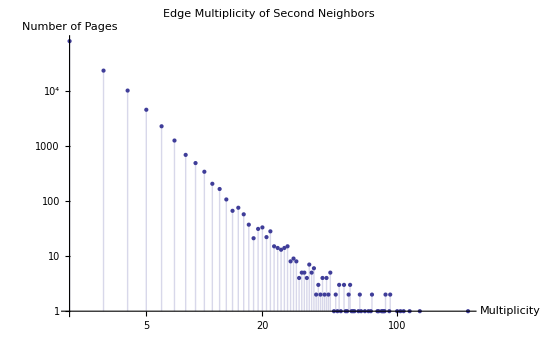

#### Number of Links Inwards The Graph

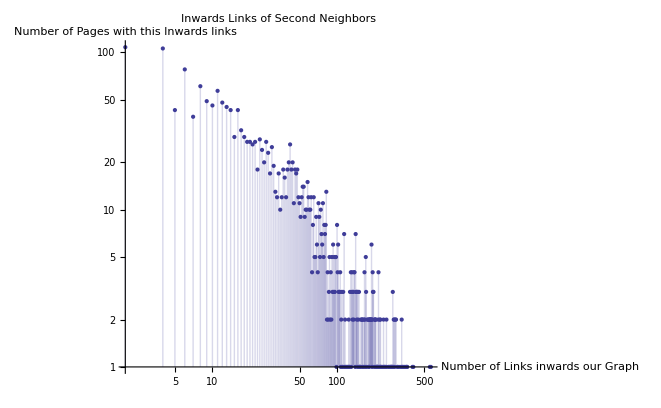

#### Number of Links Outwards The Graph

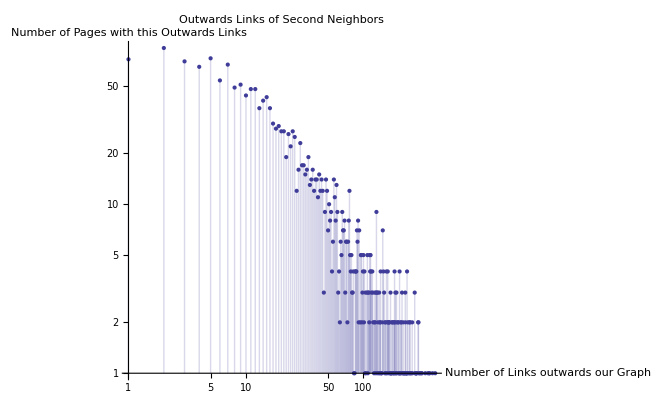

#### Distribution of Outwards Factors among Second Neighbors

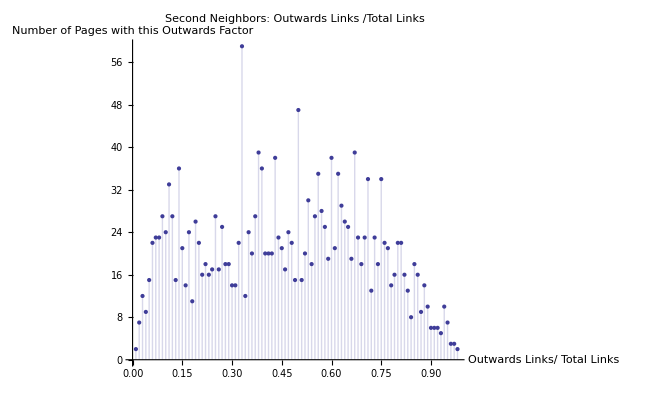

### Expansion of our Graph

#### We add to our Graph the inwards links of the second neighbors

```mathematica
StarTrekNet=NewGraphWithCorrectMultiplicity[Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/startrekNetwork/allStarTrekWeighted.tsv","TSV"]];
```

```mathematica
GoodInLinks=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/startrekNetwork/GoodInLinks.tsv","TSV"];
```

```mathematica
GoodInLinksNoSelfLoops=DeleteCases[GoodInLinks,{a_,a_,__}];
```

```mathematica
StarTrekNetExpanded=Flatten[ {StarTrekNet,GoodInLinksNoSelfLoops},1];
```

```mathematica
StarTrekNetExpanded[[4002]]
```

{Lost_(season_1),Janel_Moloney,2}

```mathematica
Length[StarTrekNetExpanded]
```

32468

```mathematica
StarTrekExpandedCorrected=NewGraphWithCorrectMultiplicity[StarTrekNetExpanded];
```

```mathematica
Export["/Users/Levantina/Documents/WOLFRAM/PROJECT/startrekNetwork/StarTrekExpandedCorrected.tsv",StarTrekExpandedCorrected,"TSV"];
```

```mathematica
StarTrekExpandedCorrected=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/startrekNetwork/StarTrekExpandedCorrected.tsv","TSV"];
```

```mathematica
STExpandedGraph= Graph[DirectedEdge@@@ (StarTrekExpandedCorrected[[All,;;2]])];
```

```mathematica
Length[VertexList[STExpandedGraph]]
```

2164

```mathematica
kcoresExpanded=Map[KCoreComponents[STExpandedGraph,#]& , Range[1,57]];
```

```mathematica
Length[Flatten[#]]& /@ kcoresExpanded
```

{2164,2063,1929,1820,1668,1561,1470,1390,1316,1235,1155,1089,999,892,737,650,587,546,519,501,479,411,405,333,330,292,286,282,275,269,256,195,179,178,176,158,157,114,114,114,67,67,66,66,66,62,61,61,61,60,60,59,59,59,59,59,59}

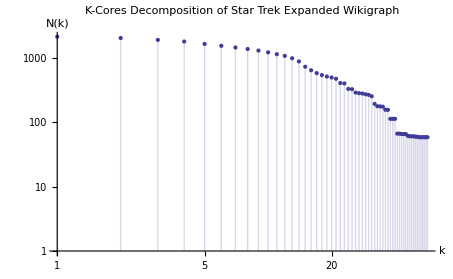

```mathematica
ListLogLogPlot[Transpose[{Range[1,57],Length[#]& @@@ kcoresExpanded}],PlotLabel->"K-Cores Decomposition of Star Trek Expanded Wikigraph", PlotRange->All,AxesLabel->{"k","N(k)"},Filling->Axis]
```

```mathematica
Subgraph[STExpandedGraph,KCoreComponents[STExpandedGraph,40],PlotLabel->"40-Core of the Expanded Wikigraph"]
```

-Graphics-

### Popularity Time Series Over a Year

#### Extract and Clean Time Series

```mathematica
{"Wednesday","Thursday","Friday","Saturday","Sunday","Monday","Tuesday"}
```

```mathematica
importedSTJanApr=readingTimeSeries["StarTrekJanToApr.txt",4];
```

```mathematica
cleanedSTJanApr=ExtractTimeSeries[importedSTJanApr,4];
```

From Wednesday:

```mathematica
dailyCorrDefault={1.0861167208459364,1.070509192186192,1.0082207459429013,0.8393580386204945,0.910410111634681,1.0716210490409843,1.0873540902600047}
```

{1.08612,1.07051,1.00822,0.839358,0.91041,1.07162,1.08735}

From Tuesday :

```mathematica
dailyCorr={1.0873540902600047,1.0861167208459364,1.070509192186192,1.0082207459429013,0.8393580386204945,0.910410111634681,1.0716210490409843};
```

```mathematica
STPopJanApr=Flatten[cleanedSTJanApr[[#,All,All,2]]]& /@ Range[1,Length[cleanedSTJanApr]];
```

```mathematica
corrSTPopJanApr=Corrections[dailyCorr,STPopJanApr];
```

From Monday:

```mathematica
dailyCorr2={1.0716210490409843,1.0873540902600047,1.0861167208459364,1.070509192186192,1.0082207459429013,0.8393580386204945,0.910410111634681};
```

```mathematica
importedSTMayDec12=readingTimeSeries["StarTrekTS2012.txt",8];
```

```mathematica
cleanedSTMayDec12=ExtractTimeSeries[importedSTMayDec12,8];
```

```mathematica
STPopMayDec12=Flatten[cleanedSTMayDec12[[#,All,All,2]]]& /@ Range[1,Length[cleanedSTMayDec12]];
```

```mathematica
corrSTPopMayDec12=Corrections[dailyCorr2,STPopMayDec12];
```

```mathematica
TimeSeriesOneYear=Flatten[{corrSTPopMayDec12[[#]],corrSTPopJanApr[[#]],PopularityCorrected[[#]] },1]& /@ Range[1,Length[corrSTPopMayDec12]];
```

```mathematica
TimeSeriesOneYearNotCorrected=Flatten[{STPopMayDec12[[#]],STPopJanApr[[#]],rightSTPop[[#]] },1]& /@ Range[1,Length[STPopMayDec12]];
```

```mathematica
Export["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/TimeSeriesOneYearNotCorrected.tsv",TimeSeriesOneYearNotCorrected,"TSV"];
```

```mathematica
Export["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/TimeSeriesOneYear.tsv",TimeSeriesOneYear,"TSV"];
```

#### One Year Time Series and Correlations

```mathematica
TimeSeriesOneYear=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/TimeSeriesOneYear.tsv","TSV"];
```

```mathematica
TimeSeriesOneYearNotCorrected=Import["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/TimeSeriesOneYearNotCorrected.tsv","TSV"];
```

```mathematica
corrOneYear=FastCorrelations[TimeSeriesOneYear];
```

```mathematica
corrOneYearNotCorrected=FastCorrelations[TimeSeriesOneYearNotCorrected];
```

```mathematica
Export["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/CorrOneYear.tsv",corrOneYear,"TSV"];
```

```mathematica
Export["/Users/Levantina/Documents/WOLFRAM/PROJECT/Timeseries/CorrOneYearNotCorrected.tsv",corrOneYearNotCorrected,"TSV"];
```

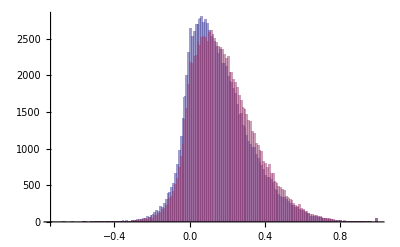

```mathematica
Histogram[{RandomSample[Flatten[corrOneYearNotCorrected],100000],RandomSample[Flatten[corrOneYear],100000]}]
```

In this histogram we can see the effect of the 0. s visitors per day that the pages that don’t exist yet. To remove this effect over the correlations we wrote this functions:

```mathematica
realLength[list_] := Length[Cases[{list}, {Longest[Repeated[0., {0,Infinity}]],x:___} :> x]];

realCorrelation[list1_, list2_] := Module[
	{reallength},
	reallength = Min[realLength[list1], realLength[list2]];
	Correlation[Take[list1, -reallength], Take[list2, -reallength]]
];

NotFastCorrelations[timeseries_]:= Outer[realCorrelation, timeseries, timeseries, 1];
```

```mathematica
TimeSeries500=TimeSeriesOneYear[[;;500]];
```

```mathematica
corrOneYear500=NotFastCorrelations[TimeSeries500];
```

Part::partw: Part 1 of {} does not exist.

Part::pspec: Part specification "All" is neither a machine-sized integer nor a list of machine-sized integers.

Complement::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

Part::pspec: Part specification "All" is neither a machine-sized integer nor a list of machine-sized integers.

Complement::heads: Heads List and Part at positions 2 and 1 are expected to be the same.

$Aborted